```mathematica
GetProbnvN1[m_,M_,gg_,wv_,lam_]:= Module[{IM,Ielec,Hv,Hb,Hg,H,nn,eval,evec,dims,psidn,wvlam,Exc},
If[m==0||gg==0||lam==0(*||gg ≤10*wv*lam^2*),
(* Set the output by hand in case g->0 because othertwise results from the calc below might not be reliable due to almost entire weight in the exciton sector *)
psidn=Table[0,{i,1,M}];
psidn[[1]]=1;
,
wvlam=wv*lam;
IM=SparseArray[{Band[{1,1}]->1},{M,M}];
Ielec=SparseArray[{Band[{1,1}]->1},{2,2}];
Exc=SparseArray[{{2,2}->1},{2,2}];

Hv=wv*SparseArray[Table[{i,i}-> i-1,{i,1,M}],{M,M}];
Hb=wvlam*SparseArray[Table[{i,i+1}-> Sqrt[i],{i,1,M-1}],{M,M}];
Hb += Transpose[Hb];
Hg=makeHg[1,m,gg];Hg += Transpose[Hg];
(*Print["Hv = ",Hv//MatrixForm];
Print["Hb = ",Hb//MatrixForm];
Print["Hg = ",Hg//MatrixForm];
Print[KroneckerProduct[Hg,IM ]//MatrixForm];
Print[Exc//MatrixForm];*)
H=KroneckerProduct[Hg,IM ]
+KroneckerProduct[Ielec,Hv]
+KroneckerProduct[Exc,Hb ];
(*Print["H = ",H//MatrixForm];*)
dims=Dimensions[H];
nn=Norm[Flatten[H]];
{eval,evec}=Eigensystem[H-nn*SparseArray[{Band[{1,1}]->1},dims],1];
eval=eval+nn;
(*Print["evec = ",evec];*)
(* conditional state for spin down *)
dims=dims[[1]]/2;(* first half basis are for spin down*)
psidn = evec[[1,1;;dims]];
psidn=Normalize[psidn];
(* probabiltiy*)
psidn=Abs[psidn]^2;
psidn//Chop;
];
psidn
];
```

```mathematica
GetProbnvN1[1,5,0.1,0.2,0.1]
```

{0.999364,0.000634843,7.98365×10^-7,1.04356×10^-9,1.27678×10^-12}

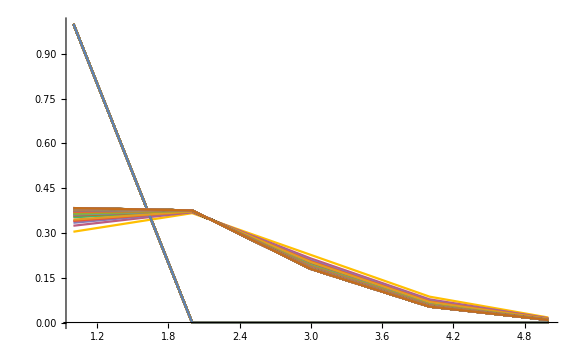

```mathematica
ListLinePlot[Flatten[Table[GetProbnvN1[m,5,gg,0.2,2],{m,0,10,2},{gg,0,50,1}],1],PlotRange->All]
```

```mathematica
ListLinePlot[Table[GetProbnvN1[1,m,gg,0.2,2],{m,1,5},{gg,0,1,1}],PlotRange->All]
```

-Graphics-

```mathematica
GetProbnvN1[1,15,0,0.2,1]
```

{30,30}

15

{0.367879,0.367879,0.18394,0.0613132,0.0153283,0.00306566,0.000510944,0.0000729919,9.12399×10^-6,1.01378×10^-6,1.01377×10^-7,9.21538×10^-9,7.6731×10^-10,5.84211×10^-11,3.63472×10^-12}

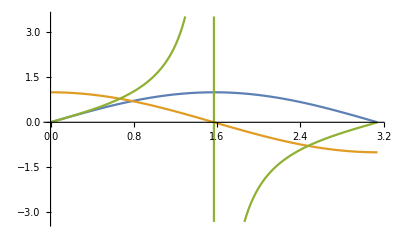

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,0,Pi}]
```